```mathematica
Animate[ParametricPlot[{If[t>0,Erfc[y/(2 √t)],0],y},{y,0,20},PlotRange -> {{-.2,1},{0,20}},AspectRatio -> 1,PlotStyle -> Thickness[0.01]],{t,-5,25}]
```

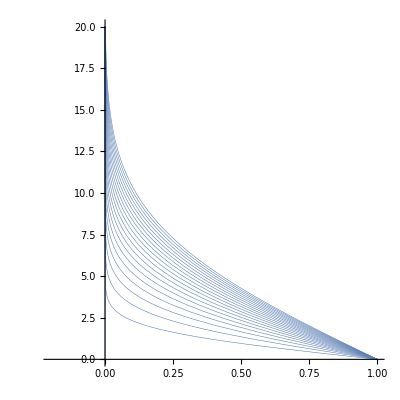

```mathematica
Show[Table[
ParametricPlot[{If[t>0,Erfc[y/(2 √t)],0],y},{y,0,20},PlotRange -> {{-.2,1},{0,20}},AspectRatio -> 1,PlotStyle -> Thickness[0.001]],{t,0,20,1}]]
```

```mathematica
Animate[ParametricPlot[{If[t>0,1/(√(π t))Exp[-y^2/(4 t)],0],y},{y,0,20},PlotRange -> {{-.2,1},{0,20}},AspectRatio -> 1,PlotStyle -> Thickness[0.01]],{t,-5,25}]
```

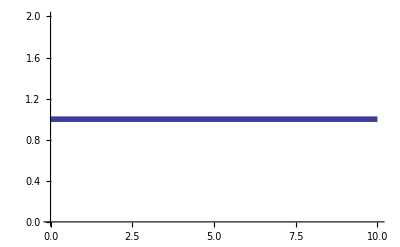

```mathematica
Plot[∫_0^∞ 1/(√(π t))Exp[-y^2/(4 t)]ⅆy ,{t,.0001,10},PlotStyle -> Thickness[0.01],PlotRange -> {All,{0,2}}]
```